-Graphics3D-

-Graphics3D-

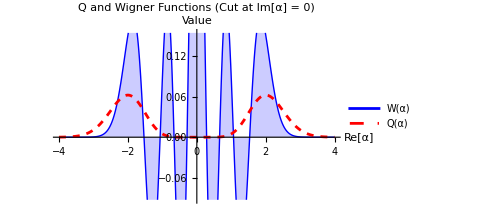

```mathematica
(*Definition of phase space coordinate variables*)(*r2 (squared radius)= |α|^2=x^2+y^2*)r2[x_,y_]:=x^2+y^2

(*--------------------------------------------------------*)
(*1. Q function (Husimi) for four-photon state|4⟩*)
(*Q(α)=1/(24π)|α|^8 Exp[-|α|^2]*)

QFunctionFourPhoton[x_,y_]:=(1/(24*Pi))*(r2[x,y]^4)*Exp[-r2[x,y]]

(*--------------------------------------------------------*)
(*2. Wigner function for four-photon state|4⟩*)
(*W(α)=2/π (-1)^n L_n(4|α|^2) Exp[-2|α|^2]*)

WignerFunctionFourPhoton[x_,y_]:=(2/Pi)*((-1)^4*LaguerreL[4,4*r2[x,y]])*Exp[-2*r2[x,y]]

(*--------------------------------------------------------*)
(*a) Plot Q function for|4⟩ state*)

Plot3D[QFunctionFourPhoton[x,y],{x,-4,4},{y,-4,4},PlotRange->All,ColorFunction->"CMYKColors",Mesh->None,AxesLabel->{"Re[α] (X1)","Im[α] (X2)","Q(α)"},PlotLabel->Style["Q Function for Four-Photon State |4⟩",Bold,14],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*b) Plot Wigner function for|4⟩ state*)
(*Need larger range to observe rings and precise height range to display positive and negative regions*)

Plot3D[WignerFunctionFourPhoton[x,y],{x,-4,4},{y,-4,4},PlotRange->{-0.2,0.7},(*Height range to show maximum positive (0.63) and negative values*)ColorFunction->"TemperatureMap",(*Color scheme that distinguishes positive and negative*)Mesh->None,AxesLabel->{"Re[α] (X1)","Im[α] (X2)","W(α)"},PlotLabel->Style["Wigner Function for Four-Photon State |4⟩ (Multiple Negative Regions)",Bold,14,Blue],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*c) 2D slice for clarity of ring structure and negative regions*)

Plot[{WignerFunctionFourPhoton[x,0],QFunctionFourPhoton[x,0]},{x,-4,4},PlotLabel->Style["Q and Wigner Functions (Cut at Im[α] = 0)",Bold,14],PlotLegends->{"W(α)","Q(α)"},AxesLabel->{"Re[α]","Value"},GridLines->{None,{0}},PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red]},Filling->{1->Axis},ImageSize->Medium]
```